```mathematica
u[t_]:=UnitStep[t]; (*converting to unit step*)
```

```mathematica
u[t];
```

```mathematica
x[t_]:=(ⅇ^(-50t)Cos[2*π*100t]+ⅇ^(-75t)Cos[2*π*200t]+ⅇ^(-100t)Cos[2*π*300t])*u[t];
```

```mathematica
x[t];
```

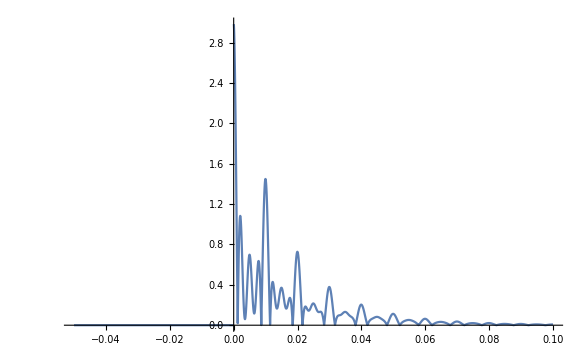

```mathematica
Plot[Abs[x[t]],{t,-0.05,0.1}, PlotRange->Full]
```

```mathematica
(*question  b*)
```

```mathematica
X[w_]:=∫_(-∞)^∞ x[t]*ⅇ^(-ⅈ*w*t)ⅆt
```

```mathematica
X[w];
```

```mathematica
(*question  c*)
```

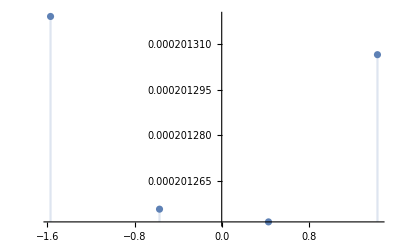

```mathematica
DiscretePlot[Abs[X[w]],{w,-π/2,π/2}](*test with pi/2*)
```

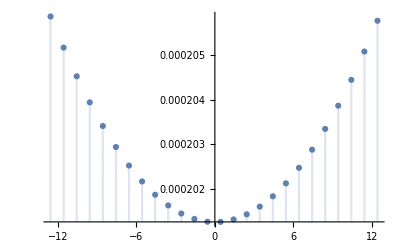

```mathematica
DiscretePlot[Abs[X[w]],{w,-4π,4π}](*test with 2pi*)
```

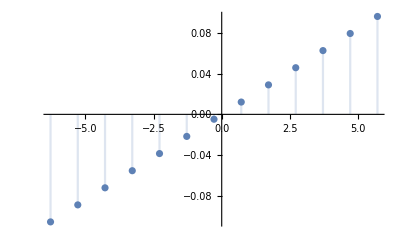

```mathematica
DiscretePlot[Arg[X[w]],{w,-2π,2π}](*Argument plot with 2pi*)
```

```mathematica
FindMaximum[X[w],{t,w}]
```

FindMaximum[X[w],{t,w}]